```mathematica
(*
 Pedro Trama Fernandes Pereira 254344
EP 3
*)
```

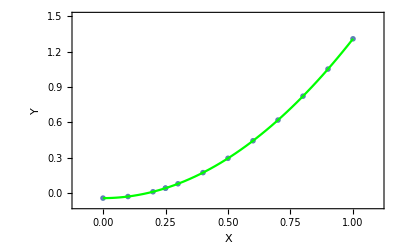

```mathematica
dados={{0.,-0.0421941},{0.1,-0.0286941},{0.2,0.0118059},{0.3,0.0793059},{0.4,0.173806},{0.5,0.295306},{0.6,0.443806},{0.7,0.619306},{0.8,0.821806},{0.9,1.05131},{1.,1.30781}};
(*
 Plotando o grafico
*)
Show[ListPlot[dados,PlotRange->{{-0.1,1.1},{-0.1,1.5}},PlotMarkers->{Magenta,Small},Frame->True,FrameStyle->Directive[Black,18],FrameLabel->{"X","Y"}],ListPlot[{{0.25,0.0421805}},PlotMarkers->{Orange,Tiny}],Plot[1.35001*x^2-6.22704*10^-6*x-0.0421936,{x,0,1},PlotRange->{{-0.1,1.1},{-0.1,1.5}},PlotStyle->Green]]
```

```mathematica
(*
 Descobrindo os valores de a, b, c, e pegando um valor de x para o Plot Marker  
*)
```

```mathematica
abc=FindFit[{{0.,-0.0421941},{0.1,-0.0286941},{0.2,0.0118059},{0.3,0.0793059},{0.4,0.173806},{0.5,0.295306},{0.6,0.443806},{0.7,0.619306},{0.8,0.821806},{0.9,1.05131},{1.,1.30781}},a x^2+b x+c,{a,b,c},x]
```

{a→1.35001,b→-6.22704×10^-6,c→-0.0421936}

```mathematica
(a x^2+b x+c)/. abc
(a x^2+b x+c)/. abc/. x->0.25
```

-0.0421936-6.22704×10^-6 x+1.35001 x^2

0.0421805